```mathematica
ListVectorPlot[{x,y},{x,-1,1,0.1},{y,-1,1,0.1}]
```

ListVectorPlot::nonopt: Options expected (instead of {y,-1,1,0.1}) beyond position 1 in ListVectorPlot[{x,y},{x,-1,1,0.1},{y,-1,1,0.1}]. An option must be a rule or a list of rules.

ListVectorPlot[{x,y},{x,-1,1,0.1},{y,-1,1,0.1}]

```mathematica
TT=Table[{-0.83304,1},{x,0,3,2},{y,-3,3,2}]
TT2=Table[{1.2004,1},{x,0,3,2},{y,-3,3,2}]
```

{{{-0.83304,1},{-0.83304,1},{-0.83304,1},{-0.83304,1}},{{-0.83304,1},{-0.83304,1},{-0.83304,1},{-0.83304,1}}}

{{{1.2004,1},{1.2004,1},{1.2004,1},{1.2004,1}},{{1.2004,1},{1.2004,1},{1.2004,1},{1.2004,1}}}

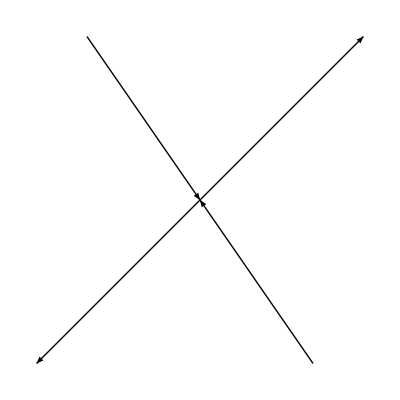

```mathematica
Block[{d=0.001},Show[
Graphics[Arrow[{{0.16,0.01},{0.16+d 1.2004,0.01+d 1}}]],
Graphics[Arrow[{{0.16,0.01},{0.16-d 1.2004,0.01-d 1}}]],Graphics[Arrow[{{0.16-d 0.83,0.01+d 1},{0.16,0.01}}]],Graphics[Arrow[{{0.16+d 0.83,0.01-d 1},{0.16,0.01}}]],AspectRatio-> 1]]
```

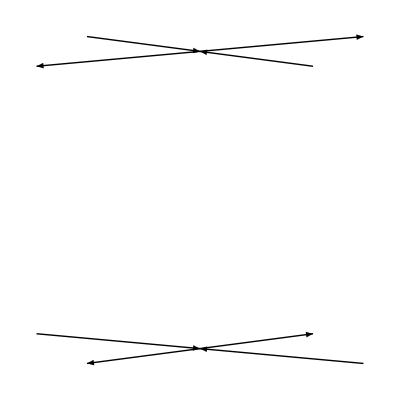

```mathematica
Block[{d=0.001},Show[
Graphics[Arrow[{{0.16,0.01},{0.16+d 1.2004,0.01+d 1}}]],
Graphics[Arrow[{{0.16,0.01},{0.16-d 1.2004,0.01-d 1}}]],Graphics[Arrow[{{0.16-d 0.83,0.01+d 1},{0.16,0.01}}]],Graphics[Arrow[{{0.16+d 0.83,0.01-d 1},{0.16,0.01}}]],Graphics[Arrow[{{0.16-d 1.2004,-0.01+d 1},{0.16,-0.01}}]],
Graphics[Arrow[{{0.16+d 1.2004,-0.01-d 1},{0.16,-0.01}}]],
Graphics[Arrow[{{0.16,-0.01},{0.16+d 0.83,-0.01+d 1}}]],
Graphics[Arrow[{{0.16,-0.01},{0.16-d 0.83,-0.01-d 1}}]]
,AspectRatio-> 1]]
```